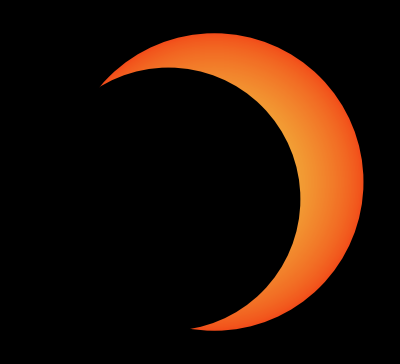

```mathematica
color=RGBColor[0.95,0.3,0.1];
n=100;
a=.75;
lune=Graphics[{
Table[{Blend[{RGBColor[0.95,0.3,0.1],RGBColor[0.95,0.9,0.3]},Rescale[r,{1,1/n},{0,1}]^a],Disk[{0.5,0},1.3r]},{r,1,1/n,-1/n}],
{Black,Disk[{0.1,-0.15},1.15]}
},Background->Transparent]
```